## Distribution plots of hedge performance

```mathematica
Clear["Global`*"]
```

```mathematica
days="90";
days="30";
```

### Customised plots

A customised Box-Whisker plot

```mathematica
ModifiedBoxWhiskerChart[d_,leg_,title_]:=Module[{s},
s=Quantile[#,{0.05,0.25, 0.5, 0.75, 0.95}]&/@Reverse[d];
BoxWhiskerChart[s, Method->{"BoxRange"->Identity},ChartLabels->Reverse[leg](*Placed[leg, Axis, Rotate[#,Pi/4]&]*), PlotTheme->"Classic", ChartStyle->Darker[Green], PlotLabel->title,PlotRange->{{-2,2},Automatic}, (*PlotRange->{{0.65,Length[leg]+0.35},{-2,2}},*)BarOrigin->Left]
]
```

The distribution chart (violin plot) has some unusual cropping in Mathematica; also, the scaling of the densities is misleading.

```mathematica
DistPlot[pos_, leg_,title_]:=Module[{d},
d=data[[pos]];
m1=Ceiling[Max[Abs[{Min[Quantile[#,0.05]&/@d], Max[Quantile[#, 0.95]&/@d]}]],0.1];
p4=DistributionChart[d,PlotTheme->"Classic",PlotRange->{-0.25,0.25},ChartLabels->{leg}, ChartStyle->Darker[Green],PlotLabel->title];
p4
]
```

### Load data

```mathematica
dataDirectory = "/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/";
prices =Import[dataDirectory <> "__prices.csv"];
```

```mathematica
nb=NotebookOpen[NotebookDirectory[] <> "boxplots_helper.nb"];
```

```mathematica
fn={
FileNames["PNL__KDE*BULLISH__4088__" <> days <> "*.csv", dataDirectory],
FileNames["PNL__KDE*CALM__8367__" <> days <> "*.csv", dataDirectory],
FileNames["PNL__KDE*COVID__9804__" <> days <> "*.csv", dataDirectory],
FileNames["PNL__SVCJ*BULLISH__4088__"<> days <> "*.csv", dataDirectory],
FileNames["PNL__SVCJ*CALM__8367__" <> days <> "*.csv", dataDirectory],
FileNames["PNL__SVCJ*COVID__9804__" <> days <> "*.csv", dataDirectory]
};

price={
Select[prices, StringContainsQ[#[[2]], "BULLISH__4088__"<> days]&][[1]][[-1]],
Select[prices, StringContainsQ[#[[2]], "CALM__8367__" <> days]&][[1]][[-1]],
Select[prices, StringContainsQ[#[[2]], "COVID__9804__" <> days]&][[1]][[-1]],
Select[prices, StringContainsQ[#[[2]], "BULLISH__4088__" <> days]&][[1]][[-1]],
Select[prices, StringContainsQ[#[[2]], "CALM__8367__" <> days]&][[1]][[-1]],
Select[prices, StringContainsQ[#[[2]], "COVID__9804__" <> days]&][[1]][[-1]]
};

fname={
"KDE_BULLISH_4088_" <> days,
"KDE_CALM_8367_" <> days,
"KDE_COVID_9804_" <> days,
"SVCJ_BULLISH_4088_" <> days,
"SVCJ_CALM_8367_" <> days,
"SVCJ_COVID_9804_" <> days
};
```

#### Call helper with each scenario

```mathematica
graphs={};
tables={};
For[kk=1, kk<=Length[fn], kk++,
data = Import[#]&/@fn[[kk]];
data=DeleteCases[Flatten[data[[#]]],_?StringQ]&/@Range[Length[data]];
data = data /price[[kk]];
legend=StringSplit[StringSplit[#,"/"][[-1]], "__"][[2;;-3]]&/@fn[[kk]];
legend=StringReplace[#, {"BLACK_SCHOLES"-> "BS", "HESTON" -> "Heston", "MERTON"->"Merton", "VARIANCE_GAMMA"->"VG", "DeltaHedge"->"Delta", "DeltaGammaHedge"->"D.-Gamma", "DeltaVegaHedge"->"D.-Vega", "MinimumVarianceHedge"->"MV"}]&/@legend;
NotebookEvaluate[nb];
AppendTo[graphs, plot];
AppendTo[tables, t3];
];
```

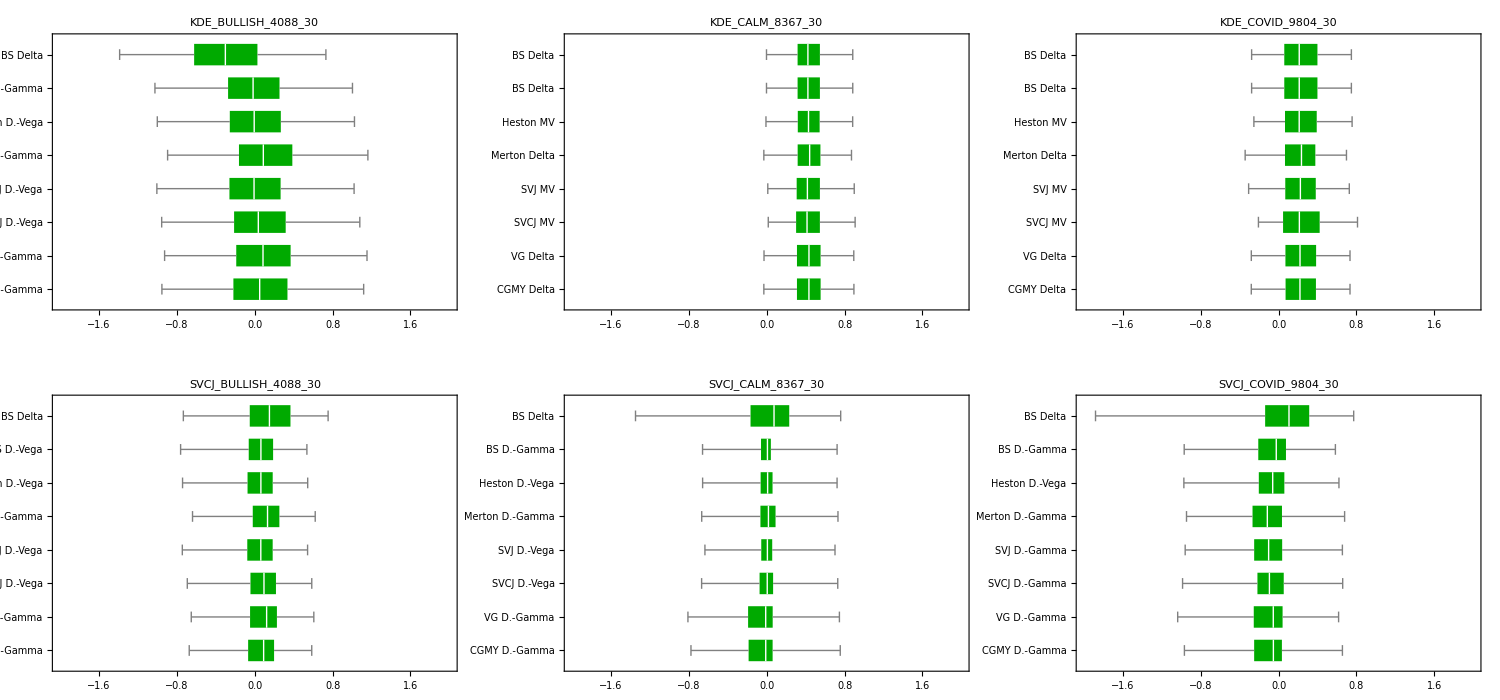

```mathematica
GraphicsGrid[{graphs[[1;;3]], graphs[[4;;6]]}, ImageSize->{1500,700}]
```

```mathematica
Export[NotebookDirectory[] <> "graphs_" <> days <> "d_all.pdf", %]
```

/Users/nat/Documents/GitHub/hedging_cc/_mathematica/graphs_30d_all.pdf

```mathematica
Table[Export[NotebookDirectory[] <> "graphs_" <> days <>"d_" <> ToString[k] <> ".pdf", graphs[[k]]], {k,1,Length[graphs]}];
```

```mathematica
{tables[[1;;3]], tables[[4;;]]}//TableForm
```

| BS Delta | BS D.-Gamma | Heston D.-Vega | Merton D.-Gamma | SVJ D.-Vega | SVCJ D.-Vega | VG D.-Gamma | CGMY D.-Gamma
Min | -3.35 | -2.58 | -2.62 | -2.48 | -2.63 | -2.59 | -2.51 | -2.53
5% ES | -1.75 | -1.34 | -1.32 | -1.21 | -1.32 | -1.27 | -1.24 | -1.27
95% ES | 1.17 | 1.49 | 1.51 | 1.65 | 1.5 | 1.57 | 1.64 | 1.61
Max | 3.31 | 5.32 | 5.29 | 5.33 | 5.28 | 5.35 | 4.77 | 5.05
Hedge error | 63.14 | 59.55 | 59.39 | 60.43 | 59.4 | 59.75 | 60.97 | 60.87 |  | BS Delta | BS Delta | Heston MV | Merton Delta | SVJ MV | SVCJ MV | VG Delta | CGMY Delta
Min | -0.94 | -0.94 | -1.01 | -1.07 | -1.03 | -1.1 | -1.16 | -1.18
5% ES | -0.16 | -0.16 | -0.17 | -0.19 | -0.15 | -0.15 | -0.2 | -0.2
95% ES | 1.04 | 1.04 | 1.05 | 1.03 | 1.07 | 1.09 | 1.08 | 1.08
Max | 1.77 | 1.77 | 1.81 | 1.8 | 1.91 | 1.86 | 1.8 | 1.81
Hedge error | 25.44 | 25.44 | 25.52 | 25.97 | 25.78 | 26.01 | 26.8 | 26.87 |  | BS Delta | BS Delta | Heston MV | Merton Delta | SVJ MV | SVCJ MV | VG Delta | CGMY Delta
Min | -1.39 | -1.39 | -1.28 | -1.38 | -1.29 | -1.23 | -1.39 | -1.39
5% ES | -0.49 | -0.49 | -0.46 | -0.55 | -0.51 | -0.39 | -0.48 | -0.48
95% ES | 0.88 | 0.88 | 0.89 | 0.83 | 0.87 | 0.96 | 0.88 | 0.88
Max | 1.37 | 1.37 | 1.39 | 1.33 | 1.38 | 1.54 | 1.44 | 1.43
Hedge error | 30.21 | 30.21 | 29.52 | 30.3 | 30.08 | 30.78 | 29.62 | 29.56
 | BS Delta | BS D.-Vega | Heston D.-Vega | Merton D.-Gamma | SVJ D.-Vega | SVCJ D.-Vega | VG D.-Gamma | CGMY D.-Gamma
Min | -11.35 | -9.46 | -9.65 | -9.69 | -9.65 | -9.58 | -8.13 | -8.07
5% ES | -1.48 | -1.16 | -1.16 | -1.06 | -1.16 | -1.12 | -1.08 | -1.1
95% ES | 1.02 | 0.98 | 0.98 | 1.11 | 0.98 | 1.04 | 1.12 | 1.1
Max | 18.69 | 20.15 | 20.46 | 20.51 | 20.46 | 20.58 | 22.56 | 24.47
Hedge error | 56.12 | 50.7 | 50.2 | 51.36 | 49.86 | 50.37 | 52.32 | 52.56 |  | BS Delta | BS D.-Gamma | Heston D.-Vega | Merton D.-Gamma | SVJ D.-Vega | SVCJ D.-Vega | VG D.-Gamma | CGMY D.-Gamma
Min | -8.07 | -4.45 | -4.45 | -5.07 | -4.45 | -4.46 | -5.04 | -6.24
5% ES | -2.2 | -1.01 | -1. | -1.01 | -0.96 | -1.01 | -1.19 | -1.14
95% ES | 1.13 | 1.12 | 1.12 | 1.13 | 1.09 | 1.13 | 1.15 | 1.17
Max | 8.81 | 8.86 | 8.88 | 12.07 | 8.88 | 9.69 | 8.73 | 9.95
Hedge error | 67.72 | 43.78 | 43.66 | 44.58 | 42.29 | 44.34 | 48.69 | 48.24 |  | BS Delta | BS D.-Gamma | Heston D.-Vega | Merton D.-Gamma | SVJ D.-Gamma | SVCJ D.-Gamma | VG D.-Gamma | CGMY D.-Gamma
Min | -16.51 | -10.93 | -10.88 | -14.36 | -14.92 | -29.05 | -24.66 | -17.07
5% ES | -3.13 | -1.64 | -1.72 | -1.76 | -1.76 | -1.84 | -1.85 | -1.75
95% ES | 1.08 | 0.98 | 1.01 | 1.09 | 1.08 | 1.11 | 1. | 1.06
Max | 7.74 | 8.92 | 7. | 21.48 | 14.13 | 20.24 | 11.11 | 11.54
Hedge error | 88.09 | 56.03 | 57.62 | 60.19 | 60.53 | 63.85 | 61.3 | 58.33

```mathematica
Export[NotebookDirectory[] <> "tables_"<> days <>"d_all.pdf", {tables[[1;;3]],{},{}, tables[[4;;]]}//TableForm]
```

/Users/nat/Documents/GitHub/hedging_cc/_mathematica/tables_30d_all.pdf

```mathematica
Export[NotebookDirectory[] <> "tables_" <> days <> "d_all.tex", {tables[[1;;3]], tables[[4;;]]}//TableForm]
```

/Users/nat/Documents/GitHub/hedging_cc/_mathematica/tables_30d_all.tex

```mathematica
models
```

{*BLACK*,*HESTON*,*MERTON*,*SVJ*,*__*__*SVCJ*,*VARIANCE_GAMMA*,*CGMY*}

```mathematica
legend=StringReplace[#, {"BLACK_SCHOLES"-> "BS", "HESTON" -> "Heston", "MERTON"->"Merton", "VARIANCE_GAMMA"->"VG", "Delta"->"D", "D.-Gamma"->"DG", "D.-Vega"->"DV"}]&/@legend;
```

```mathematica
Flatten[Position[legend[[;;,3]], "D"]]
```

{2,5,7,11,15,19,23}

```mathematica
dpos = Flatten[Position[legend[[;;,3]], "D"]];
dgpos = Flatten[Position[legend[[;;,3]], "DG"]];
dvpos = Flatten[Position[legend[[;;,3]], "DV"]];
mvpos = Flatten[Position[legend[[;;,3]], "MV"]];
```

```mathematica
legend[[dpos]]
```

(SVCJ | BS | D | COVID | 9804
SVCJ | CGMY | D | COVID | 9804
SVCJ | Heston | D | COVID | 9804
SVCJ | Merton | D | COVID | 9804
SVCJ | SVCJ | D | COVID | 9804
SVCJ | SVJ | D | COVID | 9804
SVCJ | VG | D | COVID | 9804)

```mathematica
legend[[dgpos]]
```

(SVCJ | BS | DG | COVID | 9804
SVCJ | CGMY | DG | COVID | 9804
SVCJ | Heston | DG | COVID | 9804
SVCJ | Merton | DG | COVID | 9804
SVCJ | SVCJ | DG | COVID | 9804
SVCJ | SVJ | DG | COVID | 9804
SVCJ | VG | DG | COVID | 9804)

```mathematica
legend[[dvpos]]
```

(SVCJ | BS | DV | COVID | 9804
SVCJ | Heston | DV | COVID | 9804
SVCJ | Merton | DV | COVID | 9804
SVCJ | SVCJ | DV | COVID | 9804
SVCJ | SVJ | DV | COVID | 9804)

```mathematica
legend[[mvpos]]
```

(SVCJ | Heston | MV | COVID | 9804
SVCJ | Merton | MV | COVID | 9804
SVCJ | SVCJ | MV | COVID | 9804
SVCJ | SVJ | MV | COVID | 9804)

```mathematica
models
```

{*BLACK*,*HESTON*,*MERTON*,*SVJ*,*__*__*SVCJ*,*VARIANCE_GAMMA*,*CGMY*}

```mathematica
models2={"BS", "Heston", "Merton", "SVJ", "SVCJ", "CGMY"};
```

```mathematica
pos2=Table[Flatten[Position[legend[[;;,2]], models2[[jj]]]], {jj, 1,Length[models2]}]
```

{{1,2,3},{6,7,8,9},{10,11,12,13},{18,19,20,21},{14,15,16,17},{4,5}}

```mathematica
pos2={{2,1,3}, {7,6,8,9}, {11,10,12,13}, {19,18,20,21}, {15,14,16,17}, {5,4}};
```

```mathematica
leghedge={"Delta", "Delta-Gamma", "Delta-Vega", "MV"};
```

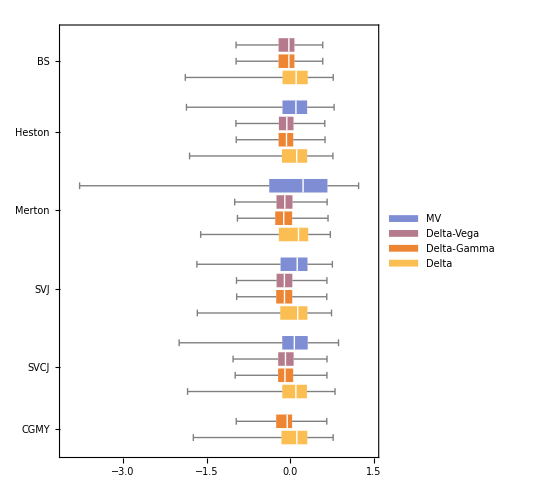

```mathematica
s=Quantile[#,{0.05,0.25, 0.5, 0.75, 0.95}]&/@d;
BoxWhiskerChart[s[[#]]&/@Reverse[pos2], Method->{"BoxRange"->Identity},(*ChartLabels->Placed[Range[1,21], Axis, Rotate[#,Pi/4]&],*)ChartLabels->{Placed[Reverse[models2],Axis],None},(* LabelingFunction->(Placed[#2.{3,1}-3,After]&),*)PlotLabel->"",(*PlotRange->{{0.65,Length[legend]+0.35},{-2.5,1}},*)BarOrigin->Left,ChartLegends->leghedge,AspectRatio->1.25,BarSpacing->{0.2,1}]
```

```mathematica
graphs={};
For[kk=1, kk<=Length[fn], kk++,
data = Import[#]&/@fn[[kk]];
data=DeleteCases[Flatten[data[[#]]],_?StringQ]&/@Range[Length[data]];
data = data /price[[kk]];
s=Quantile[#,{0.05,0.25, 0.5, 0.75, 0.95}]&/@data;
g=BoxWhiskerChart[s[[#]]&/@Reverse[pos2], Method->{"BoxRange"->Identity},(*ChartLabels->Placed[Range[1,21], Axis, Rotate[#,Pi/4]&],*)ChartLabels->{Placed[Reverse[models2],Axis],None},(* LabelingFunction->(Placed[#2.{3,1}-3,After]&),*)PlotLabel->fname[[kk]],PlotRange->{{-2,2}, Automatic},(*PlotRange->{{0.65,Length[legend]+0.35},{-2.5,1}},*)BarOrigin->Left,ChartLegends->leghedge,AspectRatio->1.25,BarSpacing->{0.2,1}];
AppendTo[graphs,g];
Export[NotebookDirectory[] <> fname[[kk]] <> "_full_graph.pdf", g]
]
```

```mathematica
Table[Export[NotebookDirectory[] <> "graphs_"<> days <> "d_full_" <> ToString[k] <> ".pdf", graphs[[k]]], {k,1,Length[graphs]}];
```